# Lesson 8: The derivative as function

```mathematica
f[x_]:=4 x^3-9x
```

```mathematica
D[f[x],x]
```

-9+12 x^2

```mathematica
f'[x] == D[f[x],x]
```

True

Plot of function and its derivative:

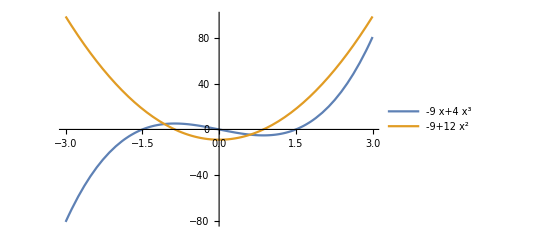

```mathematica
Plot[{Evaluate@f[x],Evaluate@D[f[x],x]},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
f[x_]:=x^2-1
```

```mathematica
f'[x]
```

2 x

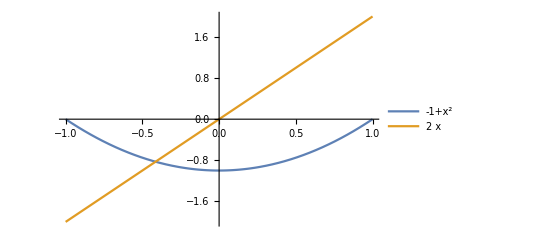
{-Graphics-,-Graphics-}

```mathematica
{Plot[Evaluate@{f[x],D[f[x],x]},{x,-1,1},PlotLegends->"Expressions"],
Plot[Evaluate@{f[x],f'[x]},{x,-1,1},PlotLegends->"Expressions"]}
```

## One-Sided Derivatives

```mathematica
g[x_]:=3RealAbs[x-5]
```

```mathematica
Limit[DifferenceQuotient[g[x],{x,h}], h->0,Direction->1]/.x->5
```

-3

```mathematica
Limit[DifferenceQuotient[g[x],{x,h}],h->0,Direction->-1]/.x->5
```

3

```mathematica
Limit[DifferenceQuotient[g[x],{x,h}],h->0,Direction->-1]
```

Piecewise[{{-3, x<5}, {3, True}}]

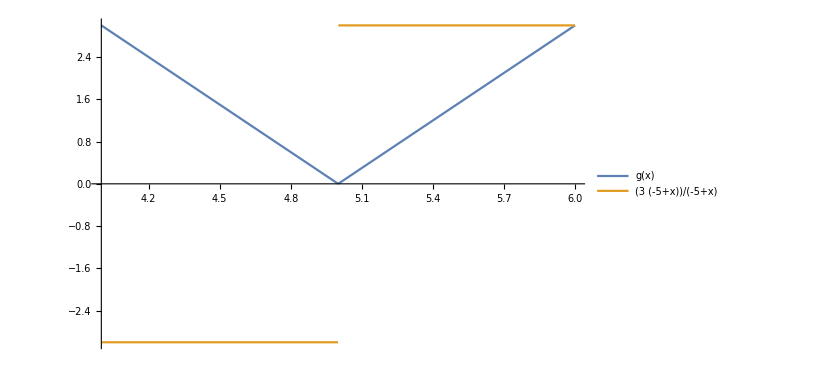

```mathematica
Plot[{g[x],Evaluate@D[g[x],x]},{x,4,6},PlotLegends->"Expressions"]
```

## Differentiability

```mathematica
f[x_]:=2RealAbs[x]
```

```mathematica
D[f[x],x]
```

(2 x)/RealAbs[x]

The function is differentiable everywhere except at 0:

```mathematica
{Limit[DifferenceQuotient[f[x],{x,h}],h->0,Direction->1]/.x->0,
Limit[DifferenceQuotient[f[x],{x,h}],h->0,Direction ->-1]/.x->0}
```

{-2,2}

```mathematica
f'[0] //Quiet
```

Indeterminate

```mathematica
D[3RealAbs[x],x]/.x->0 //Quiet
```

Indeterminate

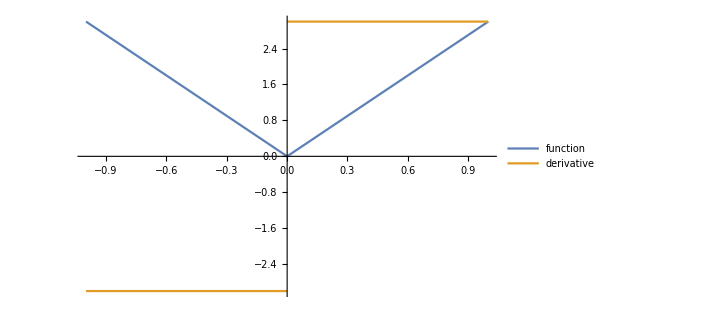

```mathematica
Plot[{3RealAbs[x],Evaluate[D[3RealAbs[x],x]]},{x,-1,1}, PlotLegends->{"function","derivative"}]
```

```mathematica
D[CubeRoot[x]^2, x]/.x->0//Quiet
```

ComplexInfinity

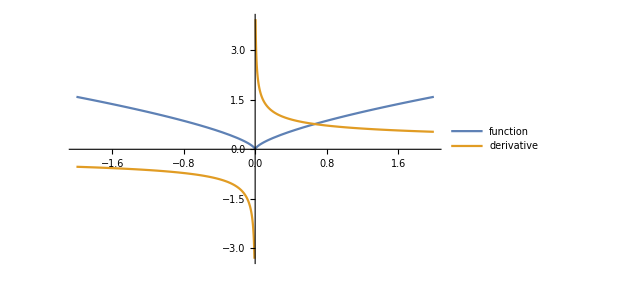

```mathematica
Plot[{CubeRoot[x]^2,Evaluate[D[CubeRoot[x]^2,x]]},{x,-2,2},PlotLegends->{"function","derivative"}]
```

## Non-differentiability 2

```mathematica
f[x_]:=Piecewise[{{x^2+1,x<0}},-2 x^2-1]
```

```mathematica
D[f[x],x]/.x->0//Quiet
```

Indeterminate

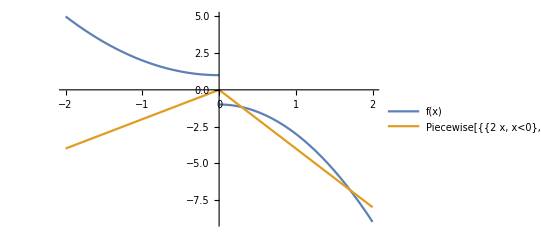

```mathematica
Plot[{f[x],Evaluate[D[f[x],x]]},{x,-2,2},PlotLegends->"Expressions"]
```

A function is non-differentiable at a vertical tangent:

```mathematica
D[CubeRoot[x],x]/.x->0//Quiet
```

ComplexInfinity

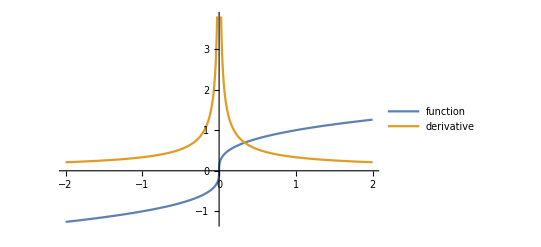

```mathematica
Plot[{CubeRoot[x],Evaluate[D[CubeRoot[x],x]]},{x,-2,2},PlotLegends->{"function","derivative"}]
```

## Higher Derivatives

```mathematica
f[x_]:=4 x^3
```

```mathematica
firstderivative = D[f[x],x]
```

12 x^2

```mathematica
secondderivative = D[firstderivative,x]
```

24 x

```mathematica
D[f[x],{x,2}]
```

24 x

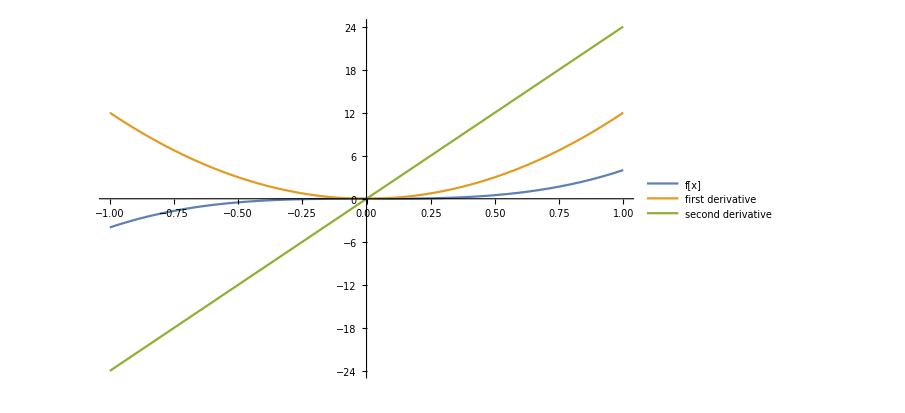

```mathematica
Plot[{f[x],firsderivative,secondderivative},
{x,-1,1},PlotLegends->{"f[x]","first derivative","second derivative"}]
```

## Higher Derivatives 2

```mathematica
f[x_]:=x^6
```

```mathematica
{d0, d1, d2,d3,d4,d5,d6}=Table[D[f[x], {x,i}],{i,0,6}]
```

{x^6,6 x^5,30 x^4,120 x^3,360 x^2,720 x,720}

```mathematica
Plot[{d0,d1,d2,d3,d4,d5,d6},{x,-3,3},PlotRange->{{-3,3},{-2000,3000}},
ImageSize->Large,PlotLabels->(Style[#,Medium]&/@{"function","first derivative",
"second derivative", "third derivative","fourth derivative","fifth derivative", "sixth derivative"})]
```

-Graphics-

## Application from Physics

The n^th derivatives for a position function s[t] are given special names:

```mathematica
s[t_]:=t^5-11t+Sin[3t]/12
```

The first six are velocity, acceleration, jerk, snap, crackle, pop:

```mathematica
{velocity, acceleration, jerk, snap, crackle, pop}=Table[D[s[t],{t,i}],{i,6}];
```

```mathematica
Plot[Evaluate[{s[t],velocity,jerk,snap,crackle,pop}],{t,0,3},Exclusions->None,PlotLabels->(Style[#,Medium]&/@{"position","velocity","acceleration","jerk","snap","crackle","pop"}),PlotRange->All]
```

-Graphics-